## Base model - analytic

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

```mathematica
DLDre[rh_,mh_,re_,me_]:=1/4 (2+(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDrh[rh_,mh_,re_,me_]:=1/4 (2-(2 (me-mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDmh[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh-re+rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
DLDme[rh_,mh_,re_,me_]:=1/4 (-2+(2 (me+mh+re-rh))/(√(me^2+2 me (mh+re-rh)+(mh-re+rh)^2)))
```

```mathematica
Solve[-DLDmh[rho,m,1,m]==DLDrh[rho,m,1,m],m]
```

{{m→1-rho}}

## Base model + global competition

```mathematica
eq1={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t]-k*nH[t]*(nH[t]+nE[t]),nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-k nH[t] (nE[t]+nH[t]),nH[0]==nH0}

```mathematica
eq2={D[nE[t],t]==me*nH[t]+(re-mh)nE[t]-k*nE[t]*(nH[t]+nE[t]),nE[0]==nE0}
```

{nE'[t]==(-mh+re) nE[t]+me nH[t]-k nE[t] (nE[t]+nH[t]),nE[0]==nE0}

```mathematica
sys={eq1,eq2}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-k nH[t] (nE[t]+nH[t]),nH[0]==nH0},{nE'[t]==(-mh+re) nE[t]+me nH[t]-k nE[t] (nE[t]+nH[t]),nE[0]==nE0}}

```mathematica
Biglambda[tmax_,nh0_,ne0_,nhf_,nef_]:=(1/tmax)*Log[(nhf+nef)/(nh0+ne0)];
```

## Functions definition

```mathematica
(*Function that takes all the Rempl parameters as arguments and returns a table of same format containing the final values of the numerical solution of the system of equations:*)
```

```mathematica
SolutionCalc[Rempl_,nE0t_,nH0t_]:=(Module[{tabT,TabRHO,TabM,TabK},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;Table[{nE[tabT[[itmax]]],nH[tabT[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->nE0t/.nH0->nH0t,{nE,nH},{t,0,tabT[[itmax]]}],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}]])
```

```mathematica
(*Function that takes all the Rempl parameters AND the solution as arguments and returns the lambda values in a table of same format as Rempl*)
```

```mathematica
LambdaCalc[Rempl_,Solu_,nE0t_,nH0t_]:=(Module[{tabT,TabRHO,TabM,TabK},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
Table[Biglambda[tabT[[itmax]], nH0t,nE0t,Solu⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,Solu⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}]])
```

```mathematica
(*Function that takes as argument the parameters Rempl and returns a list of {the solution, the corresponding lambda, sensi1,sensi2,sensi3,...}*)
```

```mathematica
SensitivityCalc[Rempl_,nE0t_,nH0t_,α_]:=(Module[{tabT,RE,TabRHO,TabM,TabK,Solu,DTabRHO,DTabM,DRHRempl,DMERempl,DMHRempl,DRHSol,DMESol,DMHSol,Lambda,DRHLambda,DMELambda,DMHLambda,SensiRH,SensiRE,SensiMH,SensiME,SensiK,TabRHdim,TabMdim},

tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
RE = Rempl⟦1,;;,1,1,2⟧[[1,2]];

TabRHdim=Table[TabRHO[[irho]],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
TabMdim=Table[TabM[[im]],{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

Solu = SolutionCalc[Rempl,nE0t,nH0t];

DTabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧+α;
DTabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧+α;

DRHRempl =Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> DTabRHO⟦irho⟧,me->TabM⟦im⟧,mh->TabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
DMERempl = Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> TabRHO⟦irho⟧,me->DTabM⟦im⟧,mh->TabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];
DMHRempl = Table[{tmax->tabT⟦itmax⟧,re->RE,rh-> TabRHO⟦irho⟧,me->TabM⟦im⟧,mh->DTabM⟦im⟧,k->TabK⟦ik⟧},{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

DRHSol = SolutionCalc[DRHRempl,nE0t,nH0t];
DMESol = SolutionCalc[DMERempl,nE0t,nH0t];
DMHSol = SolutionCalc[DMHRempl,nE0t,nH0t];

Lambda = LambdaCalc[Rempl,Solu,nE0t,nH0t];
DRHLambda = LambdaCalc[DRHRempl,DRHSol,nE0t,nH0t];
DMELambda = LambdaCalc[DMERempl,DMESol,nE0t,nH0t];
DMHLambda = LambdaCalc[DMHRempl,DMHSol,nE0t,nH0t];

SensiRH =(1/α)*(DRHLambda-Lambda);
SensiME =(1/α)*(DMELambda-Lambda);
SensiMH =(1/α)*(DMHLambda-Lambda);

{Solu,Lambda,SensiRH,SensiME,SensiMH}]

)
```

```mathematica
(*Function that takes Rempl as an argument and returns {Sensitivities (format of the previous function),Optimal strategies (of same format as Rempl)}.*)
```

```mathematica
OptimalStrategy[Rempl_,nE0t_,nH0t_,α_]:=(Module[{tabT,TabRHO,TabM,TabK,RE,Sensitivities,SensiRH,SensiME,SensiMH,Opt},
tabT=Rempl⟦;;,1,1,1,1⟧⟦;;,2⟧;
TabRHO = Rempl⟦1,;;,1,1,3⟧⟦;;,2⟧;
TabM = Rempl⟦1,1,;;,1,4⟧⟦;;,2⟧;
TabK = Rempl⟦1,1,1,;;,6⟧⟦;;,2⟧;
RE = Rempl⟦1,;;,1,1,2⟧[[1,2]];

Sensitivities = SensitivityCalc[Rempl,nE0t,nH0t,α];
SensiRH = Sensitivities[[3]];
SensiME = Sensitivities[[4]];
SensiMH = Sensitivities[[5]];

Opt=Table[Sign[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}⟦Position[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}],Max[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}]]]⟦1,1⟧⟧]*Position[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}],Max[Abs[{SensiRH⟦itmax,irho,im,ik⟧,SensiME⟦itmax,irho,im,ik⟧,SensiMH⟦itmax,irho,im,ik⟧}]]]⟦1,1⟧,{itmax,1,Length[tabT]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabK]}];

{Sensitivities,Opt}])
```

## Figure 2 panel B

```mathematica
tmaxB = {0.7,1,1.5,3};
NE0 =0.5;
NH0 = 0.5;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,0.95,0.05}];
TabM =Flatten[{Table[i,{i,0,0.05,0.005}],Table[i,{i,0.1,2.5,0.05}]}];
TabKH ={0,0.1,1};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatA=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

```mathematica
Lambda=ResultatA[[1,2]];
```

### Optimal strategies

```mathematica
OptTest=ResultatA[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{1}
 |  |  |  |

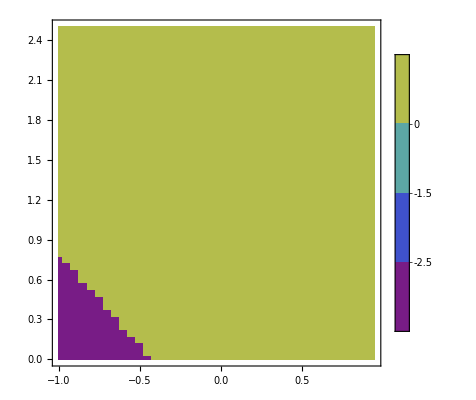
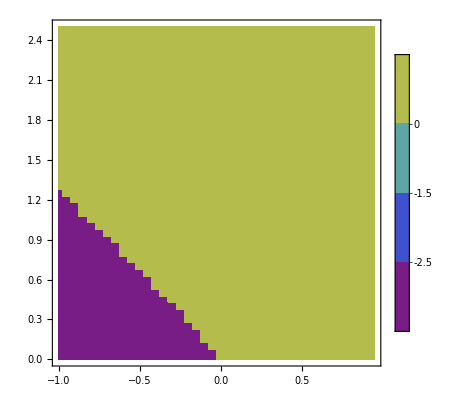
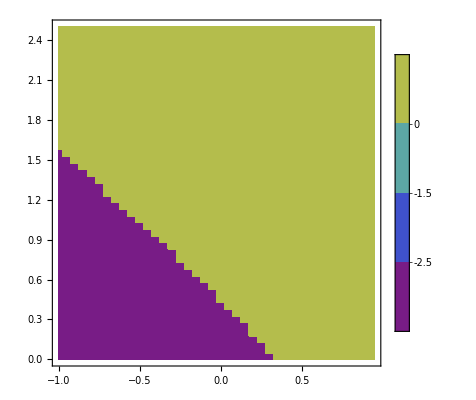
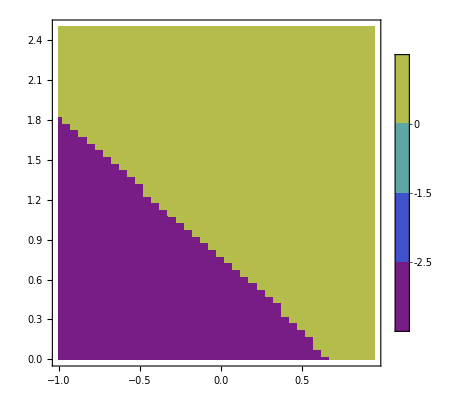

```mathematica
Table[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

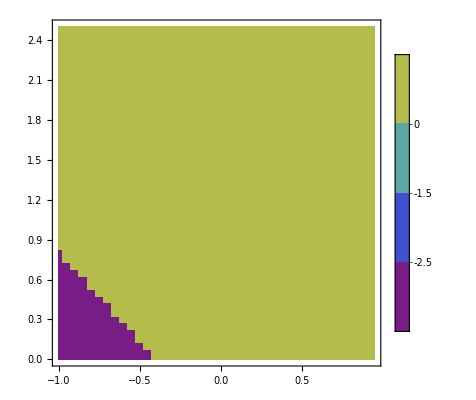
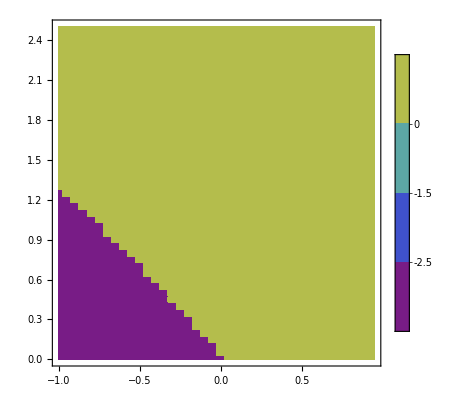
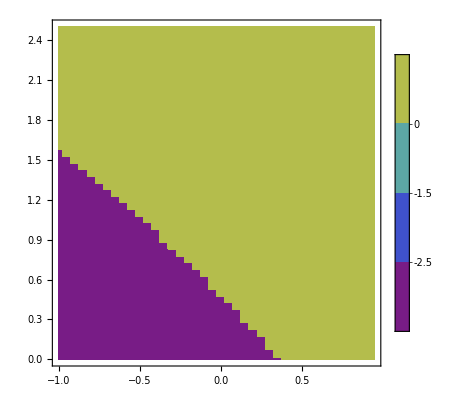
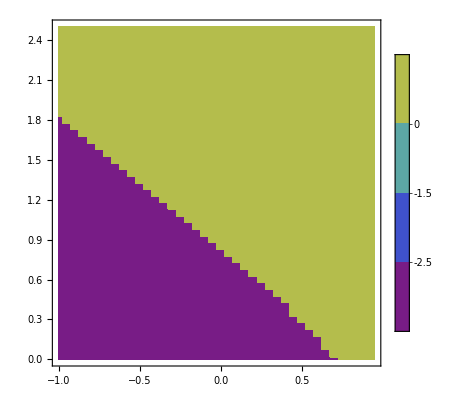

```mathematica
Table[ListContourPlot[dataOptTest⟦2,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

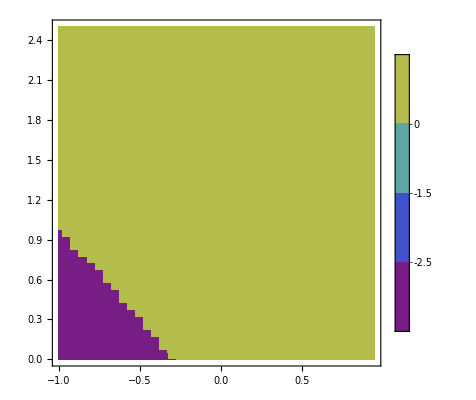
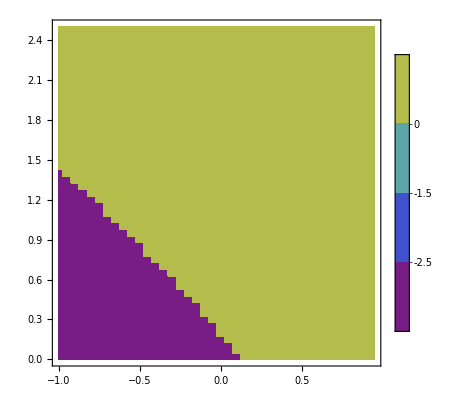
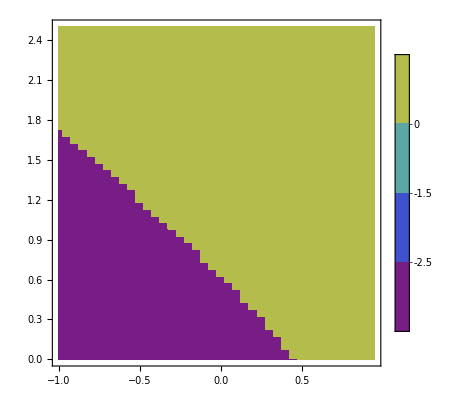
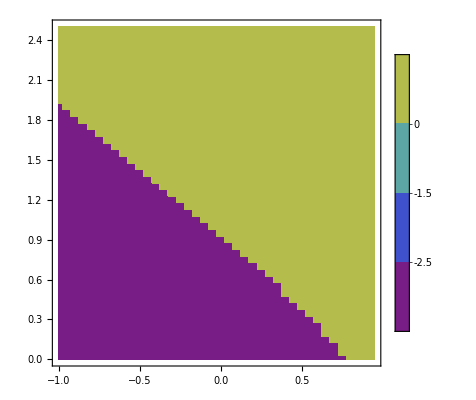

```mathematica
Table[ListContourPlot[dataOptTest⟦3,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.329526, 0.762208, 0.474596],RGBColor[0.097699, 0.498132, 0.548165],RGBColor[0.122103, 0.00901808, 0.39826]}

```mathematica
SensiRH=ResultatA[[1,3]];
```

```mathematica
SensiMH=ResultatA[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiRH[[itmax]][[irho]][[im]][[ik]]/SensiMH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

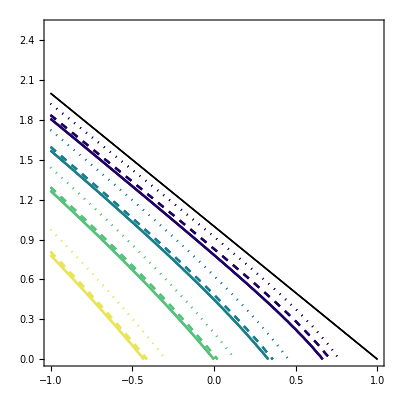

```mathematica
Show[Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]],Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[2,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{0.5,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]],Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[3,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dotted],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]]
```

## Figure 2 panel C - Extract some Lambda parametric maps

```mathematica
Lambda=ResultatA[[1,2]];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],Lambda[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

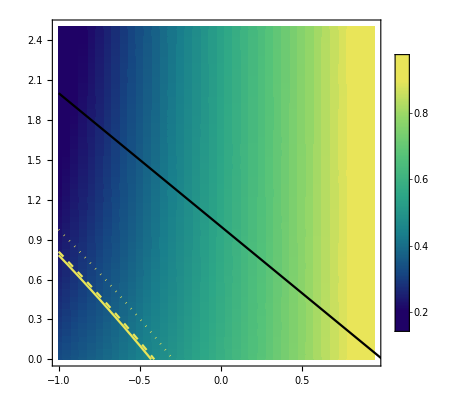

```mathematica
Show[ListDensityPlot[dataLambda⟦1,1⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,0.9}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],ListContourPlot[dataSensiRatio[[1,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[1]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[2,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[1]],Thickness[0.004],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[3,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[1]],Thickness[0.004],Opacity[1],Dotted],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

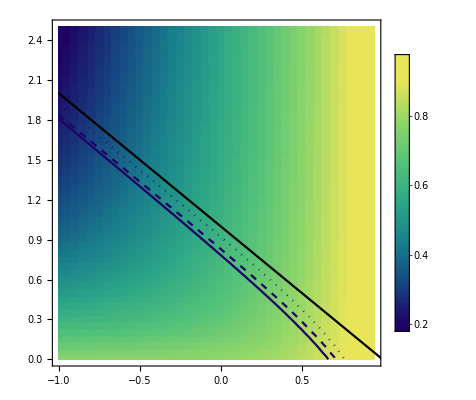

```mathematica
Show[ListDensityPlot[dataLambda⟦1,4⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,0.9}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]],
ListContourPlot[dataSensiRatio[[1,4]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[4]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[2,4]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[4]],Thickness[0.004],Opacity[1],Dashed],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[3,4]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[4]],Thickness[0.004],Opacity[1],Dotted],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],LabelStyle->{FontSize->18,FontFamily->"Arial",Black}]
```

## Supplementary figure 2 panel A

```mathematica
tmaxB = {0.7,1,1.5,3};
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{Table[i,{i,0,0.05,0.005}],Table[i,{i,0.1,2.5,0.05}]}];
TabKH ={0,0.1,1};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatB=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatB[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{1}
 |  |  |  |

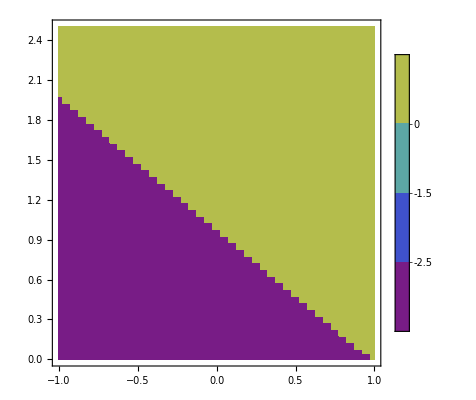
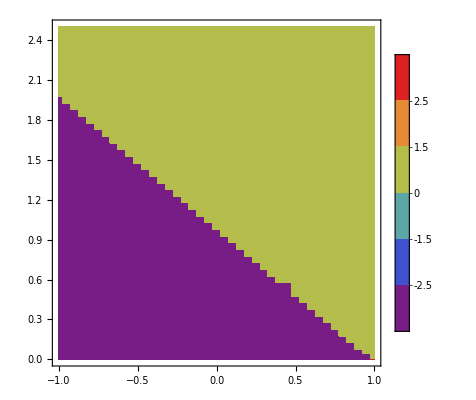
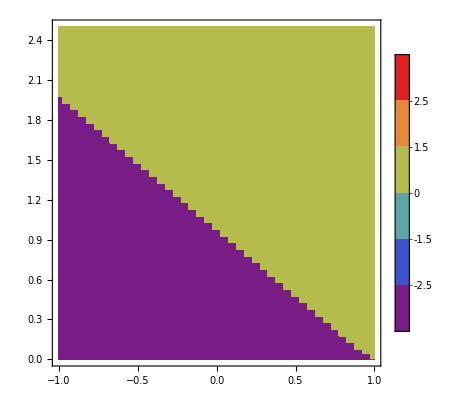
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

```mathematica
Table[ListContourPlot[dataOptTest⟦2,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[dataOptTest⟦3,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.329526, 0.762208, 0.474596],RGBColor[0.097699, 0.498132, 0.548165],RGBColor[0.122103, 0.00901808, 0.39826]}

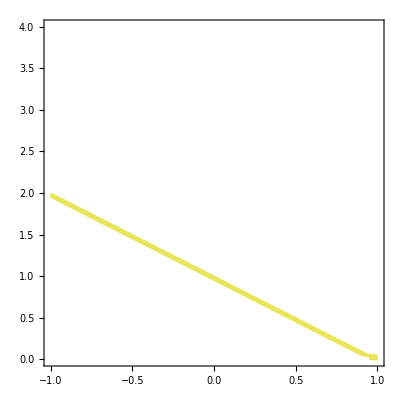
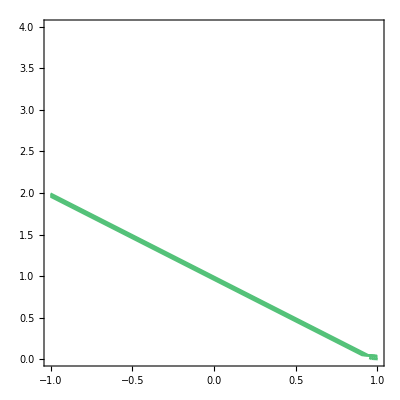
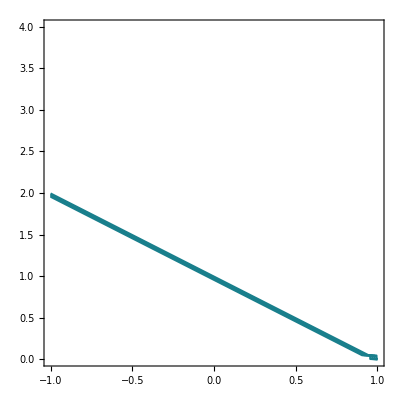

```mathematica
Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]
```

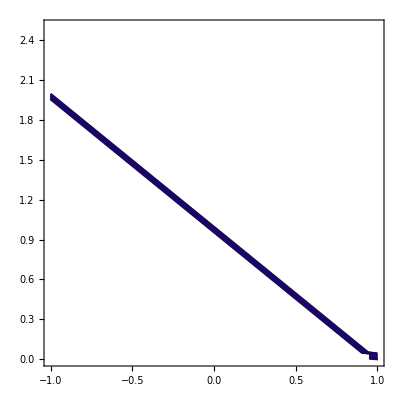

```mathematica
Show[Table[ListContourPlot[dataOptTest[[3,itmax]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],{itmax,1,Length[tmaxB]}]]
```

```mathematica
SensiRH=ResultatB[[1,3]];
```

```mathematica
SensiMH=ResultatB[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

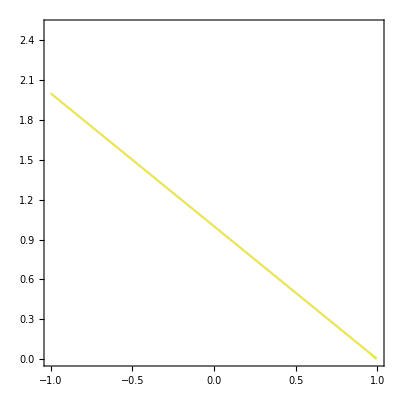
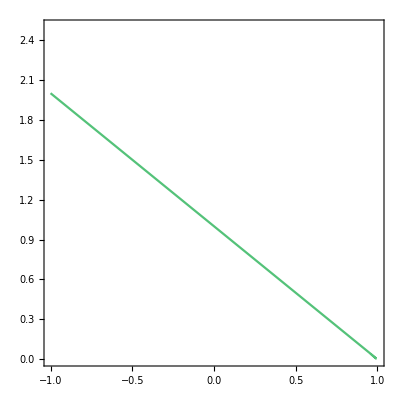
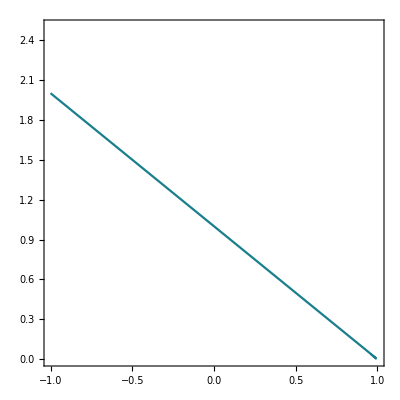
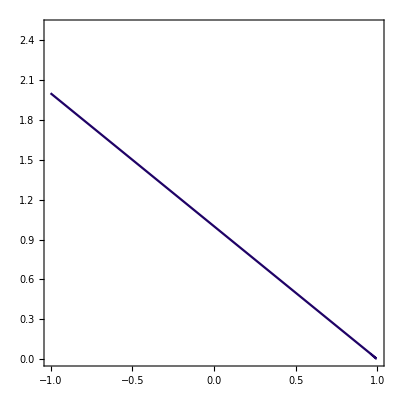

```mathematica
Table[Show[ListContourPlot[dataSensiRatio[[2,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]
```

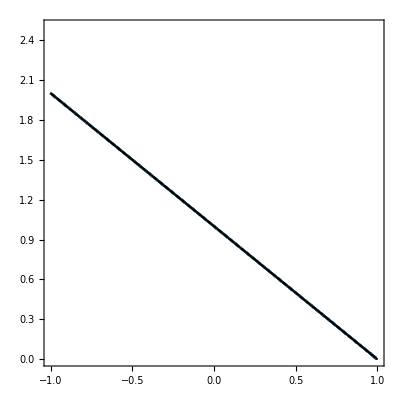

```mathematica
Show[Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]],Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[2,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{0.5,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]],Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[3,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dotted],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]]
```

## Supplementary figure 2 - panel B

```mathematica
tmaxB = {1,3,5};
NE0 =0;
NH0 = 1;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.025}];
TabM =Flatten[{Table[i,{i,0,0.05,0.005}],Table[i,{i,0.1,2.5,0.025}]}];
TabKH ={0,0.1,1};
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,k-> TabKH⟦ikh⟧},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
ResultatC=OptimalStrategy[Rempl,NE0,NH0,0.0001];
```

### Optimal strategies

```mathematica
OptTest=ResultatC[[2]];
```

```mathematica
dataOptTest=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],OptTest[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}]
```

{1}
 |  |  |  |

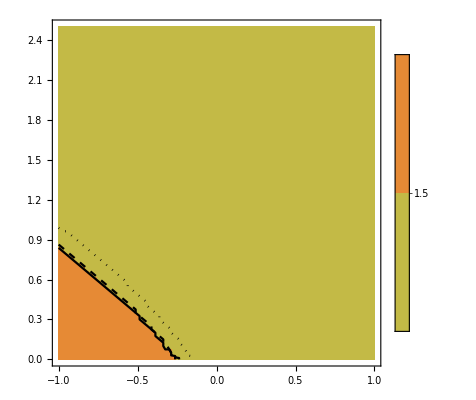
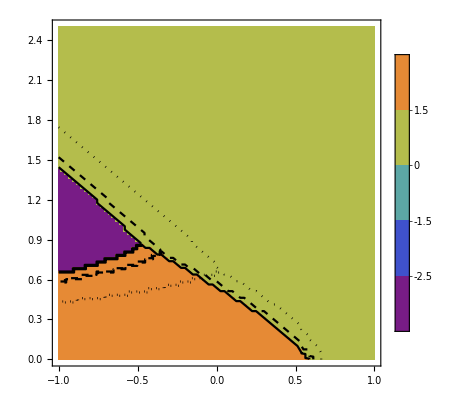
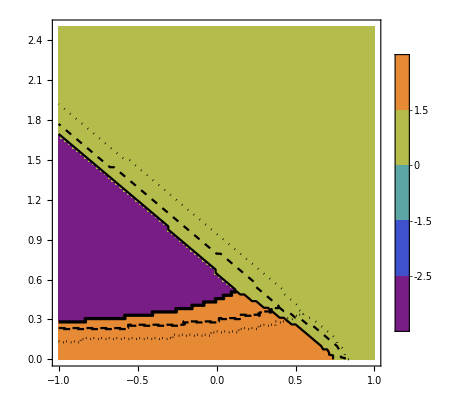

```mathematica
Table[Show[ListContourPlot[dataOptTest⟦1,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],ListContourPlot[dataOptTest[[1,itmax]],ContourShading->None,Contours->{0,1.5},ContourStyle->Directive[Black,Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataOptTest[[2,itmax]],ContourShading->None,Contours->{0,1.5},ContourStyle->Directive[Black,Dashed,Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataOptTest[[3,itmax]],ContourShading->None,Contours->{0,1.5},ContourStyle->Directive[Black,Dotted,Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]
```

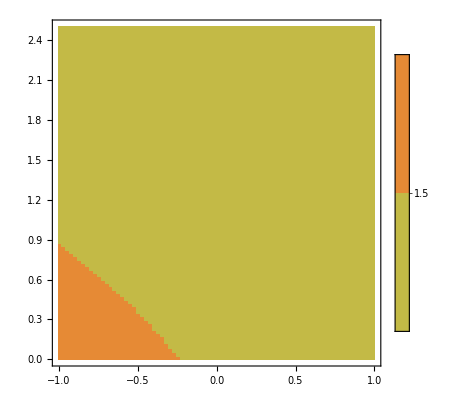
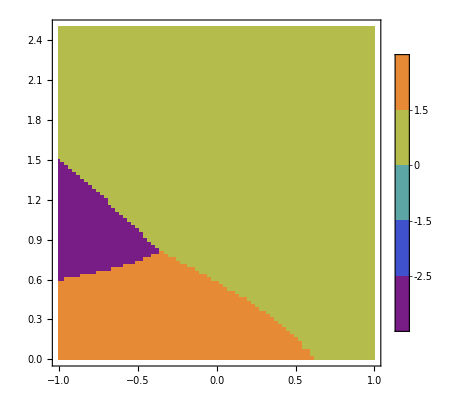
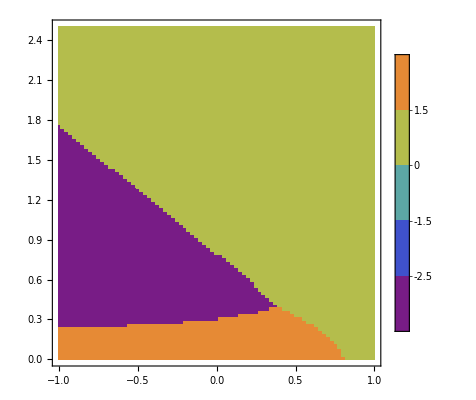

```mathematica
Table[ListContourPlot[dataOptTest⟦2,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

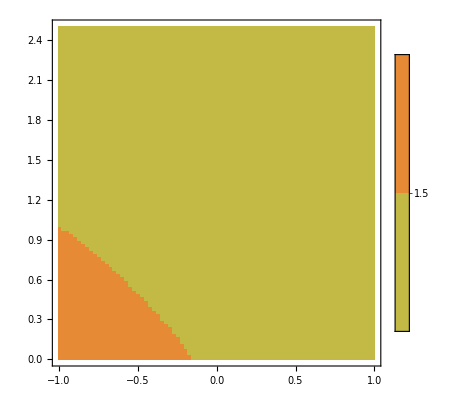
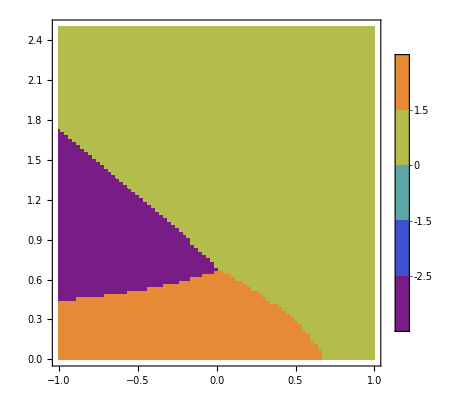
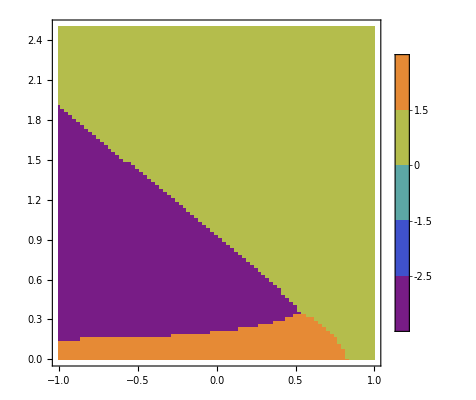

```mathematica
Table[ListContourPlot[dataOptTest⟦3,itmax⟧,Mesh->None,InterpolationOrder->0,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{-3,3}]]&),PlotLegends->Automatic,PlotRange->All,BaseStyle->{FontSize->16},Contours->{-2.5,-1.5,0,1.5,2.5}],{itmax,1,Length[tmaxB]}]
```

## ContourPlot

```mathematica
listcolor=Reverse[Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]]
```

{RGBColor[0.914809, 0.897673, 0.350652],RGBColor[0.175507, 0.652273, 0.528496],RGBColor[0.122103, 0.00901808, 0.39826]}

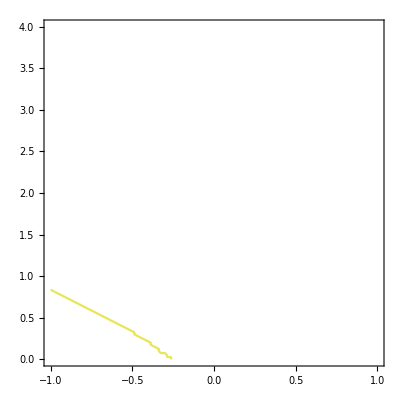
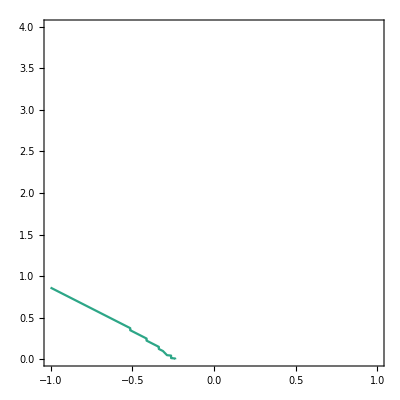
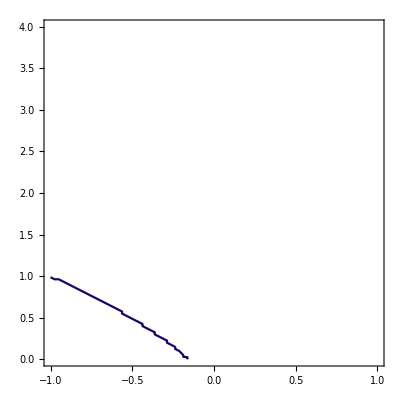

```mathematica
Table[ListContourPlot[dataOptTest[[ik,1]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,4}}],{ik,1,Length[TabKH]}]
```

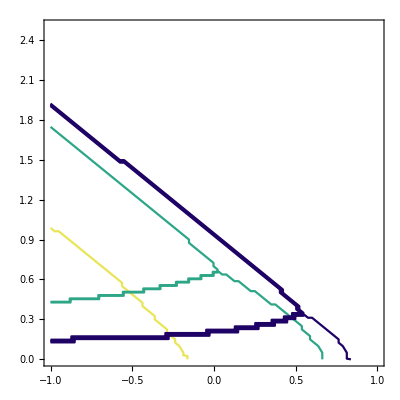

```mathematica
Show[Table[ListContourPlot[dataOptTest[[3,itmax]],ContourShading->None,Contours->{-4.5,-3.5,-2.5,-1.5,-0.5,0.5,1.5,2.5,3.5,4.5},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],{itmax,1,Length[tmaxB]}]]
```

```mathematica
SensiRH=ResultatC[[1,3]];
```

```mathematica
SensiME=ResultatC[[1,4]];
```

```mathematica
SensiMH=ResultatC[[1,5]];
```

```mathematica
dataSensiRatio=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiMH[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio2=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiME[[itmax]][[irho]][[im]][[ik]]/SensiRH[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]},{itmax,1,Length[tmaxB]}];
```

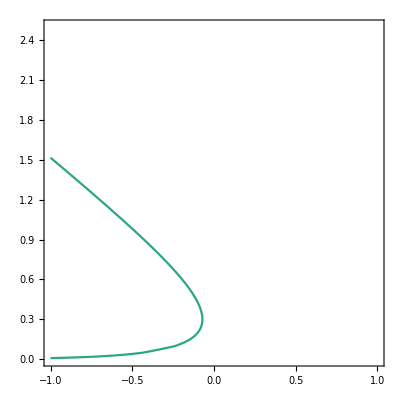
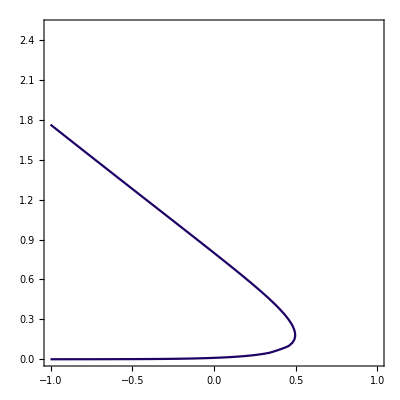
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[ListContourPlot[dataSensiRatio[[2,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]
```

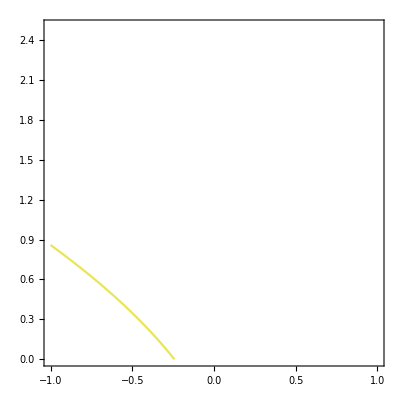
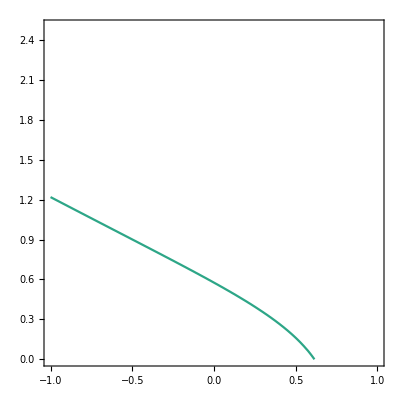
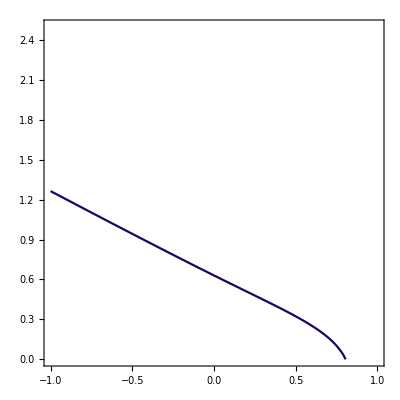

```mathematica
Table[Show[ListContourPlot[dataSensiRatio2[[2,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]
```

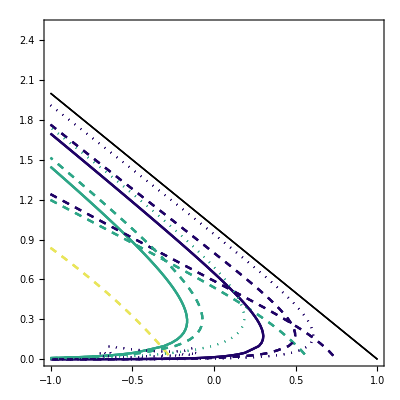

```mathematica
Show[Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio2[[1,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]],Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[2,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{0.5,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]],Show[Table[Show[Table[Show[ListContourPlot[dataSensiRatio[[3,itmax]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dotted],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}],ListContourPlot[dataSensiRatio[[1,itmax]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],LabelStyle->{FontSize->18,FontFamily->"Arial",Black},Frame->True,PlotRange->{{-1,1},{-0.0001,2.5}}]],{itmax,1,Length[tmaxB]}]],{ik,1,Length[TabKH]}],Plot[1-rho,{rho,-1,1},PlotStyle->Directive[Black,Thick]]]]
```